Supplemental notebook to 
Richard  Herrmann, 
Fractional Calculus - Introduction for Physicists,
4th edition, 
World Scientific Publishing, Singapore. 
Chapter 7
https://www.worldscientific.com/worldscibooks/10.1142/14345#t=aboutBook

# Zeros of solutions of the free fractional wave equation

Richard Herrmann

gigaHedron, r.herrmann@gigahedron.fractionalcalculus.org

February 2025.

## Introduction

Mathematica notebook presenting  solution to exercise 7.1
Find the zeros within the range $0.51 < \alpha < 1.5$ and $0.05 < x < 15 $  of the solutions of the free fractional wave equation for the Fourier-, Riemann- and Caputo definitions of a fractional derivative.

## Program ex7.1.B.30.nb

### start clean, set precision, make pdf-files, set start time

```mathematica
Clear[alpha];
prec = 5;
exportDataType="pdf";
start = AbsoluteTime[];
```

### set home directory ~/results

```mathematica
hdir=FileNameJoin[{$HomeDirectory,"results"}];
If[Not@FileExistsQ[hdir],CreateDirectory[hdir]];
SetDirectory[hdir]
```

C:\Users\r\results

### Riemann zeros of fractional equivalent of trigonometric solutions

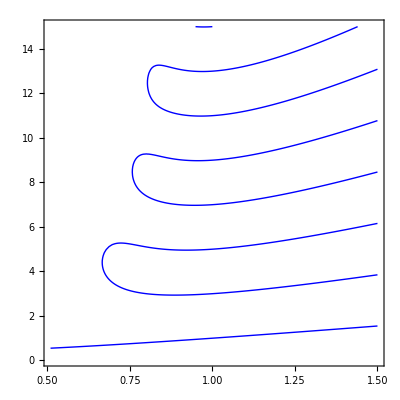

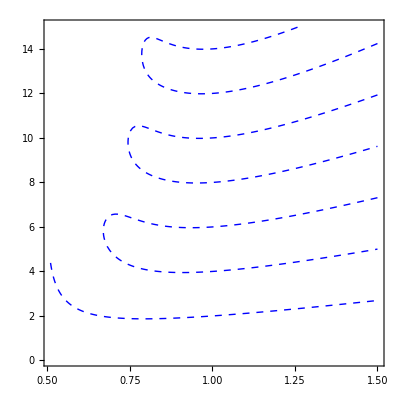

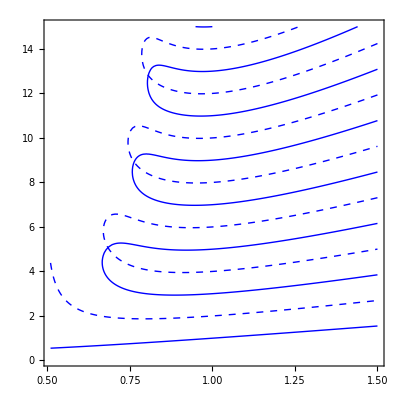

HOZeroesRie.pdf

```mathematica
name = "HOZeroesRie";
sinR[x_] = x^(2 alpha -1)MittagLefflerE[2 alpha, 2 alpha, -x^(2 alpha)];
cosR[x_] = x^(alpha-1)MittagLefflerE[2 alpha,  alpha, -x^(2 alpha)];
pcR = ContourPlot[cosR[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Blue,Thick},MaxRecursion->prec]
psR = ContourPlot[sinR[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Blue,Dashed,Thick},MaxRecursion->prec]
fout = Show[{pcR,psR}]
Export[name<>"."<>exportDataType,fout]
```

### Caputo zeros of fractional equivalent of trigonometric solutions

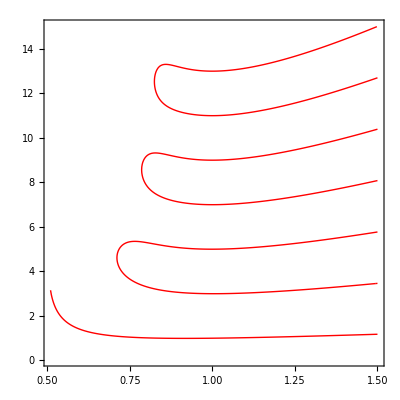

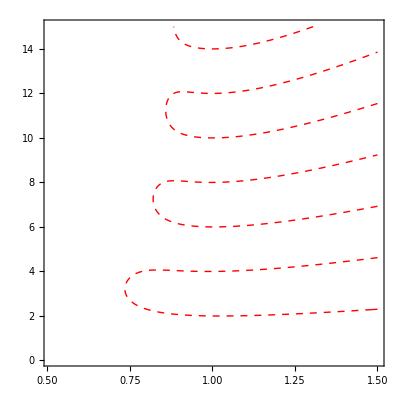

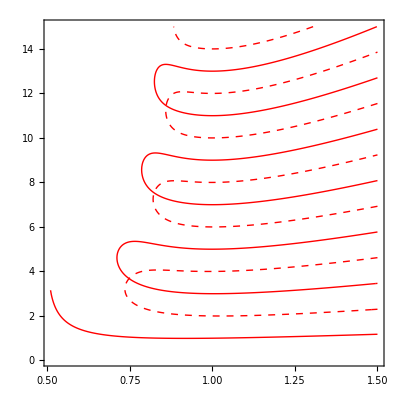

HOZeroesCap.pdf

```mathematica
name = "HOZeroesCap";
sinC[x_] = x^(alpha)MittagLefflerE[2 alpha, 1+ alpha, -x^(2 alpha)];
cosC[x_] = MittagLefflerE[2 alpha, -x^(2 alpha)];
pcC = ContourPlot[cosC[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Red,Thick},MaxRecursion->prec]
psC = ContourPlot[sinC[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Red,Dashed,Thick},MaxRecursion->prec]
fout = Show[{pcC,psC}]
Export[name<>"."<>exportDataType,fout]
```

### compare both and export plots

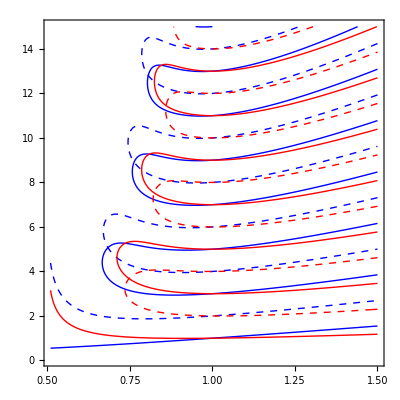

```mathematica
totalRC = Show[{pcR,psR,pcC,psC}]
```

### Fourier zeros of fractional equivalent of trigonometric solutions

ⅇ^((ⅈ π)/(2 alpha))

ⅇ^(-(ⅈ π)/(2 alpha))

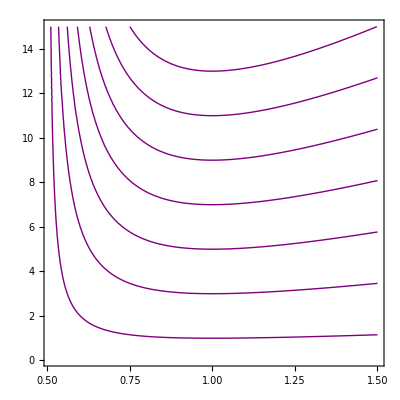

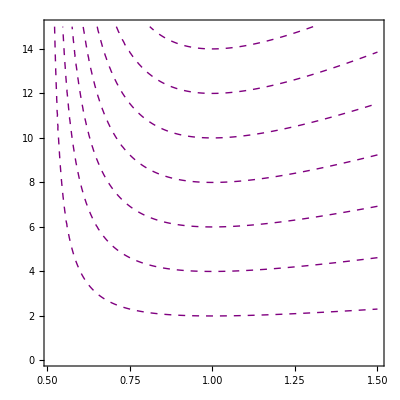

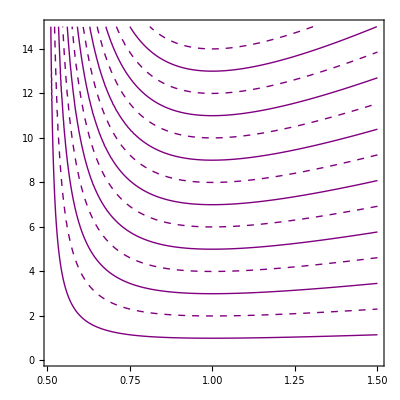

HOZeroesFou.pdf

```mathematica
name = "HOZeroesFou";
fp =  Exp[+I Pi/( 2alpha)]
fm =  Exp[-I Pi/( 2alpha)]
sinF[x_] = 1/(2 I)(Exp[fp x]- Exp[fm x]);
cosF[x_] = 1/2(Exp[fp x]+ Exp[fm x]);
pcF = ContourPlot[cosF[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Purple,Thick},MaxRecursion->prec]
psF = ContourPlot[sinF[x Pi/2]==0,{alpha,0.51,1.5},{x,0.05,15},ContourStyle->{Purple,Dashed,Thick},MaxRecursion->prec]
fout = Show[{pcF,psF}]
Export[name<>"."<>exportDataType,fout]
```

### compare and export all: Riemann, Caputo, Fourier

totalRCF

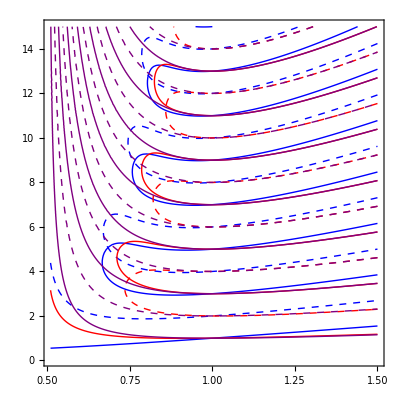

totalRCF.pdf

```mathematica
name = "totalRCF"
totalRCF = Show[{pcR,psR,pcC,psC,pcF,psF}]
Export[name<>"."<>exportDataType,totalRCF]
```

### final

```mathematica
stop = AbsoluteTime[];
Print["time used :", IntegerPart[stop-start], " sec"]
```

time used :854 sec